```mathematica
NumberOfSteps = 9;
a=1;V[x_,y_,z_]:= Sum[(16 Subscript[V, 0])/(n×m×π^2)×Sin[(n×π)/a x]×Sin[(m×π)/a y]×Sinh[π/a×√(n^2+m^2)×z]/Sinh[π √(n^2+m^2)],{n,1,2×NumberOfSteps+1,2},{m,1,2×NumberOfSteps+1,2}]
N[V[a/2,a/2,a/2]]
```

0.166667

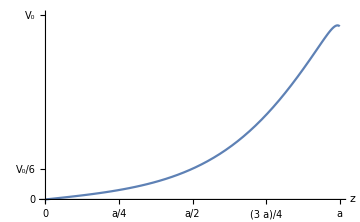

```mathematica
Subscript[V, 0]=1;
Plot[
V[a/2,a/2,z],{z,0,a},
AxesLabel->Automatic, Ticks->{{0,{a/4,"a/4"},{a/2,"a/2"},{(3a)/4,"(3  a)/4"},{a,"a"}},{0,{Subscript[V, 0]/6,"V_0/6"},{Subscript[V, 0],"V_0"}}}, PlotRange->{{0,a},{0,Subscript[V, 0]}},
GridLines->{{a/2},{Subscript[V, 0]/6}},
ImageSize->Medium
]
```

```mathematica
Plot3D[
V[a/2,y,z],{y,a/4,(3a)/4},{z,0,a},
AxesLabel->Automatic, Ticks->{
{0,{a/4,"a/4"},{a/2,"a/2"},{(3a)/4,"(3  a)/4"},{a,"a"}},{0,{a/4,"a/4"},{a/2,"a/2"},{(3a)/4,"(3  a)/4"},{a,"a"}},
{0,{Subscript[V, 0]/6,"V_0/6"},{Subscript[V, 0],"V_0"}}},
 PlotRange->{{0,a},{0,Subscript[V, 0]}}, ImageSize->Medium
]
```

-Graphics3D-